## Benford’s Law

#### Task

Write a routine to calculate the distribution of first significant digits in a collection of numbers, then display actual vs. expected distribution in the way most convenient for your language.

P(d)=Log_10(1+1/d)

Use the first 1000 numbers from the Fibonacci sequence  as your data set.

```mathematica
benford[list_List]:=Show[Histogram[First@*IntegerDigits/@list],
Plot[Length[list]Log10[1+1/d],{d,1,9}]
]
```

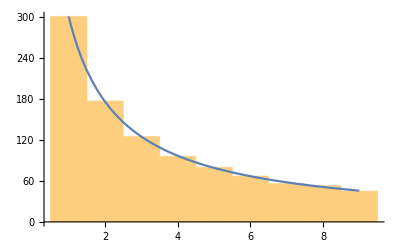

```mathematica
benford[Table[Fibonacci[n],{n,1000}]]
```

## Balanced Brackets

#### Task

Generate a string N opening brackets [ and with N closing brackets ], in some arbitrary order.

Determine whether the generated string is balanced, that is, whether it consists entirely of pairs of opening/ closing brackets, none of which mis-nest.

```mathematica
bracketsClose[s_String]:=MemberQ[{"","[]"},
FixedPoint[StringReplace[#,"["~~Shortest[x___]~~"]"->x]&,s]]
```

```mathematica
genBrackets[n_Integer]:=
With[{replacements=RandomSample[Range[2*n],n]},
StringJoin[Range[2*n]/.Join[AssociationThread[#[[1]],"["],AssociationThread[#[[2]],"]"]]]&@GatherBy[Range[2*n],MemberQ[replacements,#]&]
]
```

```mathematica
Grid[Table[{#,bracketsClose[#]}&@genBrackets[15],10]]
```

[][[[]][]][[]][[][]][]][][[]][ | False
[][][[[[[]]][]][]]][[[[[[]]]]] | False
[[]][]]]][][[][[]][]][[[[]][][ | False
[[]][][][][][[]]]]][][[[[[]][] | False
[][]]][]]]][][][][[][[][[[[]][ | False
[[[]][][[[]][[]]][][[]][][]][] | True
[][]]]][]][[[[][[][][]][][[]][ | False
[[]]]]]][[[[[[][][[[[]][][]]]] | False
[[][[[[]][[]]]]]]]][[[[]][]][[ | False
[[][[]][][]][[[]]]][]][[][[[]] | False

```mathematica
BaseForm[]
```